```mathematica
ⅇ^4-π/3*√6/(14/5)
```

ⅇ^4-(5 π)/(7 √6)

```mathematica
N[ⅇ^4-(5 π)/(7 √6)]
```

53.682

```mathematica
With[{d=N[53.68204301160005/°]},Defer[d °]]
```

3075.75 °

```mathematica
N[3075.7545002044385 °]
```

53.682

```mathematica
ScientificForm[53.68204301160006]
```

5.3682×10^1

```mathematica
π//Cos
```

-1

```mathematica
Table[(n^2-n+2)/(3*n^2+2*n-4),{n,1,10}]
```

{2,1/3,8/29,7/26,22/81,8/29,44/157,29/102,74/257,23/79}

```mathematica
Table[i*j,{i,3},{j,4}]
%//MatrixForm
```

{{1,2,3,4},{2,4,6,8},{3,6,9,12}}

(1 | 2 | 3 | 4
2 | 4 | 6 | 8
3 | 6 | 9 | 12)

```mathematica
Table[i*j,{i,3},{j,4}]%//MatrixForm
```

(1 | 4 | 9 | 16
4 | 16 | 36 | 64
9 | 36 | 81 | 144)

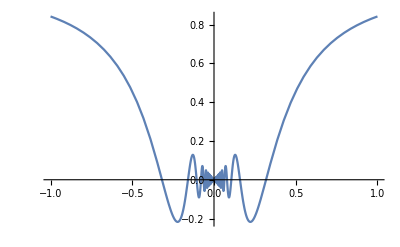

ParametricPlot

PolarPlot

Set::write: 0. xy 中的标签 Times 被保护.

ListPlot

```mathematica
Plot[x*Sin[1/x],{x,-1,1}]

ParametricPlot

PolarPlot

ContourPlot[xy(x^2-y^2)=2,{x,-10,10},{y,-10,10}]
ListPlot
```

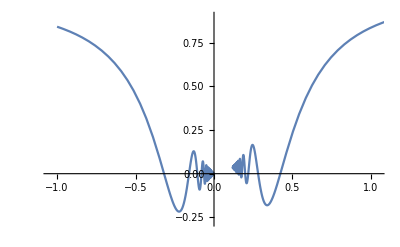

ParametricPlot

PolarPlot

ContourPlot

ListPlot

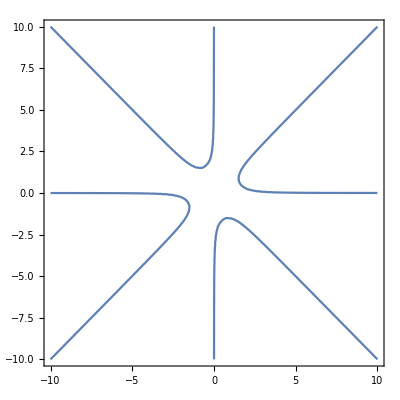

```mathematica
ContourPlot[x*y*(x^2-y^2)==2,{x,-10,10},{y,-10,10}]
```

```mathematica
Plot3D[x*y*(x^2-y^2),{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{t*Cos[t],t*Sin[t],t},{t,0,100}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{3*v*Cos[u],3*v*Sin[u],0.3*u*v},{u,0,5*Pi},{v,0,6}]
```

-Graphics3D-

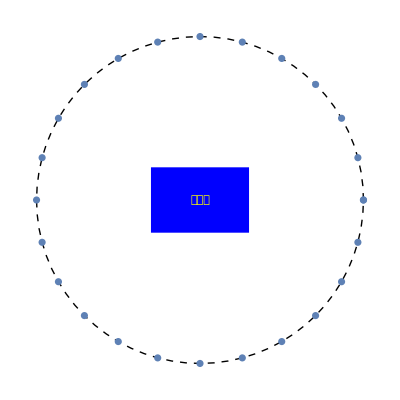

```mathematica
Show[
Graphics[{Dashed,Circle[],
Blue,Rectangle[{-0.3,-0.2},{0.3,0.2}],
Yellow,Text["点列图",{0,0}]}],
ListPlot[
Table[{Cos[t],Sin[t]},{t,0,2*Pi,Pi/12}],
PlotStyle->{Gray，PointSize[0.05]},
AspectRatio->Automatic
]
]
```